0.05

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

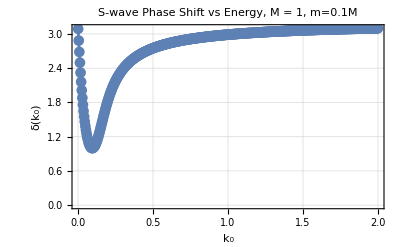

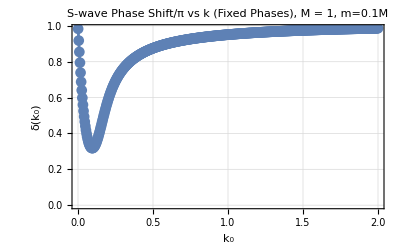

-0.0248496-4.38179 x^2-1.8531 x^4

-0.0192522+11.7885 x^2

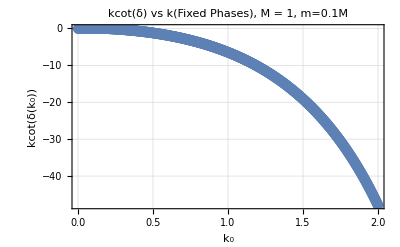

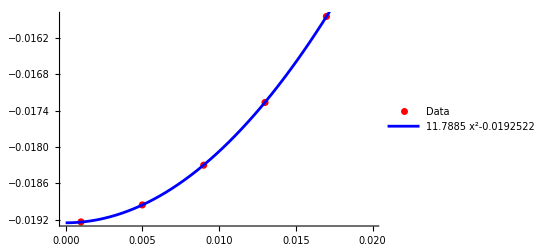

```mathematica
(*---PARAMETERS---*)
M=1;                (* Mass of Nucleon*)
m=0.1*M;               (*Pion mass*)
m2=0.05*M
α=1;              (*Depth of Yukawa potential*)
β=0.9*α;
r0=10^-6;          (*Small value near r=0 for boundary condition*)

kMin = m/100;
kMax = 20*m; 
kSpacing = (kMax-kMin)/500(*0.01*m^2*);
λ = 2*Pi/Abs[m]; (* De Broglie Wavelength*)
rMax=10*λ;           (*Max radius for numerical integration, ensures asymptotic behavior by being much larger than λ*)
fitStart=0.8*rMax;       (*Start of asymptotic region*)
fitEnd=rMax;         (*End of asymptotic region*)
fitSpacing = rMax/100;    (* Interval spacing in asymptotic region*)

(*---Yukawa Potential---*)
V[r_]:=-α*Exp[-m*r]/r+β*Exp[-m2*r]/r;

(*---Phase Shift Extractor---*)
ClearAll[extractPhaseShift]

extractPhaseShift[k0_?Positive,M_?Positive]:=Module[{k,sol,uFunc,data,fit,δ},k=k0;
(*Numerical solution to Schrödinger equation*)sol=NDSolve[{u''[r]==(M*V[r]-k0^2) u[r],u[r0]==r0,u'[r0]==1},u,{r,r0,rMax},MaxSteps->Infinity];
(*Wavefunction interpolator*)uFunc=Function[r,Evaluate[u[r]/. sol[[1]]]];
(*Sample numerical wavefunction in asymptotic region*)data=Table[{r,uFunc[r]},{r,fitStart,fitEnd,fitSpacing}];
(*Fit to A*Sin[k*r+δ] to extract phase shift*)fit=NonlinearModelFit[data,A*Sin[k*r+δ],{{A,1},{δ,0}},r,MaxIterations->∞]; (*MaxIterations->∞*)
(*Return δ modulo π (optional,depending on context)*)Mod[δ/. fit["BestFitParameters"],Pi](*δ/.fit["BestFitParameters"]*)]

extractPhaseShift1[k0_?Positive,rm_?Positive,M_?Positive]:=Module[{k,sol,uFunc,data,fit,δ},k=k0;
(*Numerical solution to Schrödinger equation*)sol=NDSolve[{u''[r]==(M*V[r]-k0^2) u[r],u[r0]==r0,u'[r0]==1},u,{r,r0,rm},MaxSteps->Infinity];
(*Wavefunction interpolator*)uFunc=Function[r,Evaluate[u[r]/. sol[[1]]]];
(*Sample numerical wavefunction in asymptotic region*)data=Table[{r,uFunc[r]},{r,0.8*rm,rm,rm/100}];
(*Fit to A*Sin[k*r+δ] to extract phase shift*)fit=NonlinearModelFit[data,A*Sin[k*r+δ],{{A,1},{δ,0}},r,MaxIterations->∞]; (*MaxIterations->∞*)
(*Return δ modulo π (optional,depending on context)*)Mod[δ/. fit["BestFitParameters"],Pi](*δ/.fit["BestFitParameters"]*)]

(*---Phase Shift Curve Generator---*)
kRange=Range[kMin,kMax,kSpacing];  (*k's to test*)
rMaxList =(10*(2 Pi/#))&/@kRange;
pairs = Transpose[{kRange,rMaxList}];

(*phaseShiftData=Table[{k0,extractPhaseShift[k0,M]},{k0,kRange}];*)

(* ---Loop through the values of k_n and rmax_n to construct the data--- *)
phaseShiftData1=ParallelTable[{kRange[[i]],extractPhaseShift1[kRange[[i]],rMaxList[[i]],M]},{i,Length[kRange]}]; 

(* ---Make the phases continuous by gluing together the pieces--- *)
unwrapPhaseReverse[data_]:=Module[{ks,deltas,unwrapped,shifts,jumpIndices},{ks,deltas}=Transpose[data];
unwrapped=deltas;
Do[If[unwrapped[[i]]-unwrapped[[i-1]]>Pi/2,(*Apply+π to all previous values*)unwrapped[[1;;i-1]]+=Pi;],{i,2,Length[unwrapped]}];
Transpose[{ks,unwrapped}]];

phaseShiftData1Unwrapped=unwrapPhaseReverse[phaseShiftData1];

extractPhaseShift[m/100,M];
extractPhaseShift1[kRange[[1]],rMaxList[[1]],M];

(*---Plot the phase shift vs k---*)
(*ListLinePlot[phaseShiftData,PlotMarkers->Automatic,AxesLabel->{"k₀","δ(k₀)"},PlotLabel->Row[{"S-wave Phase Shift vs Energy, M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,{-1,3Pi}}]*)
ListLinePlot[phaseShiftData1,PlotMarkers->Automatic,AxesLabel->{"k₀","δ(k₀)"},PlotLabel->Row[{"S-wave Phase Shift vs Energy, M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,All}]
(*ListLinePlot[phaseShiftData1Unwrapped,PlotMarkers->Automatic,AxesLabel->{"k₀","δ(k₀)"},PlotLabel->Row[{"S-wave Phase Shift vs k (Fixed Phases), M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,All}]*)
ListLinePlot[{#[[1]],#[[2]]/Pi}&/@phaseShiftData1Unwrapped,PlotMarkers->Automatic,AxesLabel->{"k₀","δ(k₀)"},PlotLabel->Row[{"S-wave Phase Shift/π vs k (Fixed Phases), M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,All}]

xmax=0.02;
kcotd = {#[[1]],#[[1]]*Cot[#[[2]]]}&/@phaseShiftData1Unwrapped;
kcotdlowk=Select[kcotd,#[[1]]<=xmax&];
cotdrootIm= {#[[1]],Cot[#[[2]]]}&/@phaseShiftData1Unwrapped;
(*scatlen= {#[[1]],-#[[2]]}&/@phaseShiftData1Unwrapped;-del[0,V0,0.001]/0.001*)

kcotdfit = Fit[kcotd,{1,x^2,x^4},x]
kcotdfitlowk= Fit[kcotdlowk,{1,x^2},x]

ListLinePlot[kcotd,PlotMarkers->Automatic,AxesLabel->{"k₀","kcot(δ(k₀))"},PlotLabel->Row[{"kcot(δ) vs k(Fixed Phases), M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,All}]
(*ListLinePlot[cotdrootIm,PlotMarkers->Automatic,AxesLabel->{"k₀","kcot(δ(k₀))"},PlotLabel->Row[{"kcot(δ) vs k(Fixed Phases), M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,All}]*)

Show[ListPlot[kcotdlowk,PlotStyle->Red,PlotLegends->{"Data"}, PlotRange->{{0,xmax},Automatic}],Plot[kcotdfitlowk,{x,0,xmax},PlotStyle->Blue,PlotLegends->{ToString[TraditionalForm[kcotdfitlowk]]}]]
```

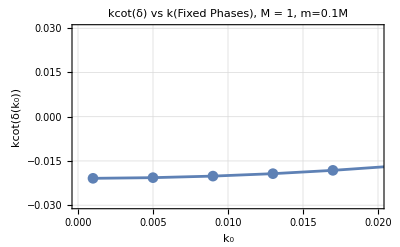

```mathematica
Show[%2772,PlotRange->{{0,0.02},{-0.03,0.03}}]
```